```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=8.6173324*10^-3;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/4801Ang"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
cPlotData=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
zPlotData=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
```

```mathematica
CarbonPotentialEinsteinHarmonic
```

{{-0.00968,0.48},{0,0},{0,0},{0.00968,0.48}}

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
V[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]
V[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[1,12,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
(*Zirconium*)
V[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[2,12,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
```

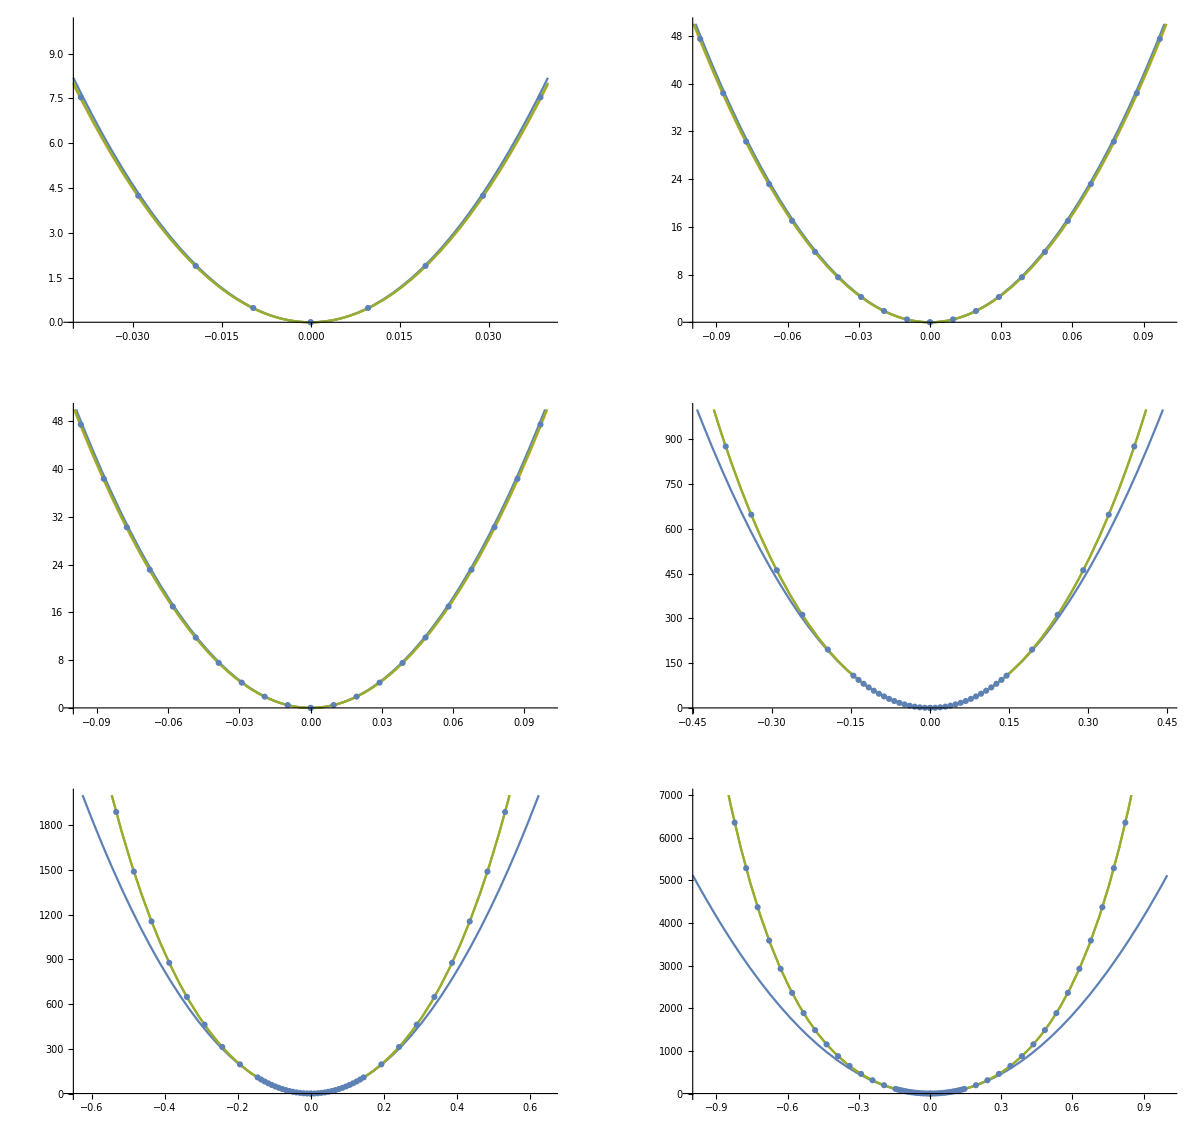

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@cPlotData],Show[P0,ListPlot@cPlotData]},{Show[P1,ListPlot@cPlotData],Show[P2,ListPlot@cPlotData]},{Show[P3,ListPlot@cPlotData],Show[P4,ListPlot@cPlotData]}},ImageSize->1200]
```

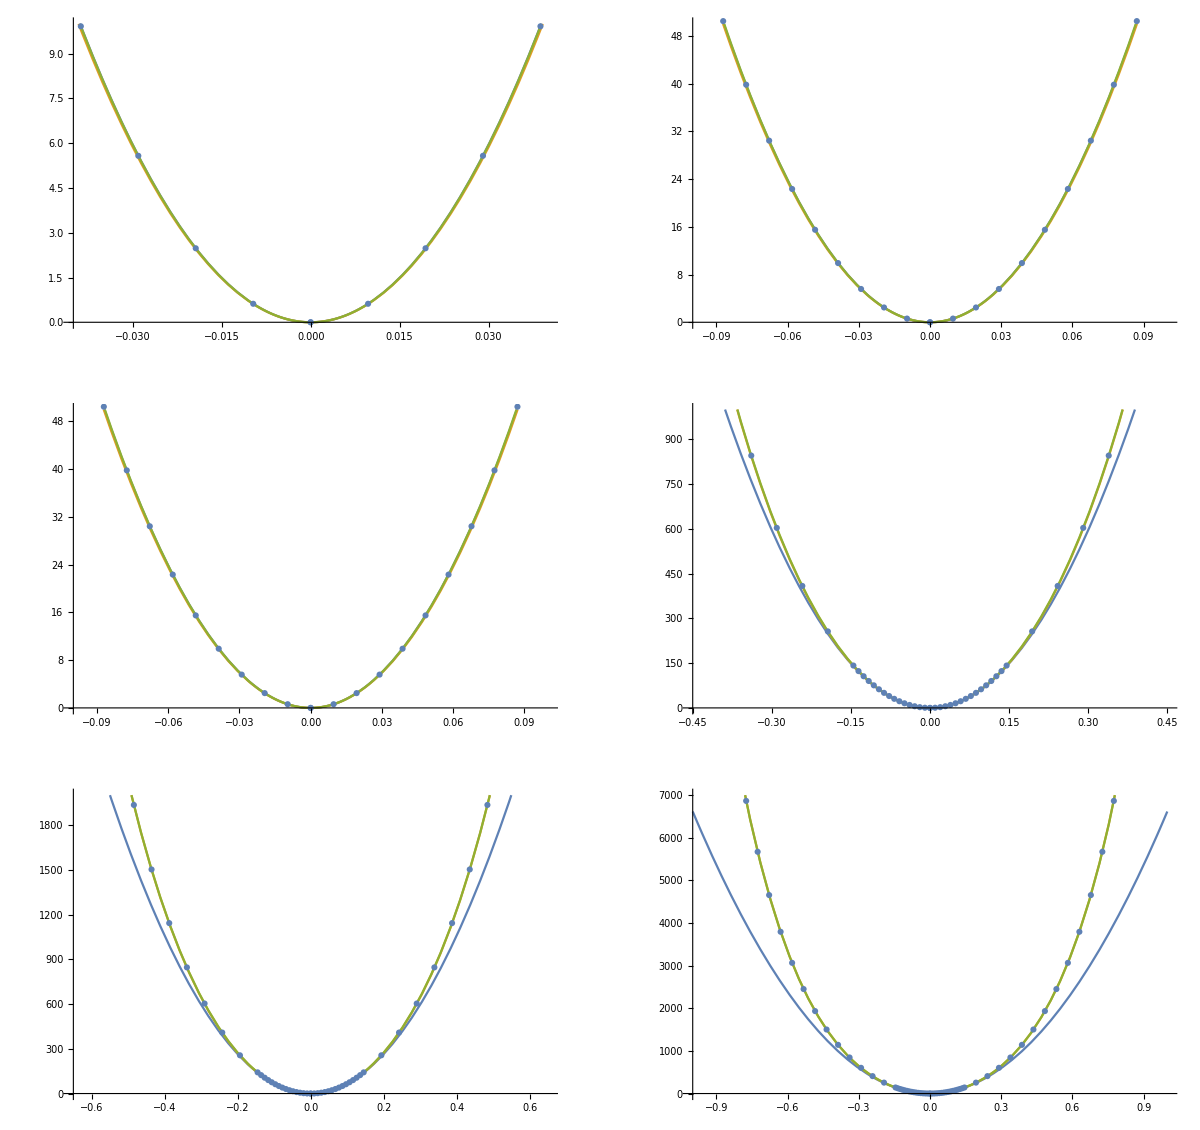

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@zPlotData],Show[P0z,ListPlot@zPlotData]},{Show[P1z,ListPlot@zPlotData],Show[P2z,ListPlot@zPlotData]},{Show[P3z,ListPlot@zPlotData],Show[P4z,ListPlot@zPlotData]}},ImageSize->1200]
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=V[1,2,x][[1]]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=V[2,2,x][[1]]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

5122.6

cOmega0 in meV/Ang**2/AMU is approximately

29.2063

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

6616.69

Z_Omega_0 in meV/Ang**2/AMU is approximately

12.0443

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒall=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,2}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,2}];
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒall[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
```

```mathematica
(*Carbon and Zironcium eigenenergies*)
(*Indexed like 1 is harmonic, 2 is 4th order ... 6 is 12th order*)
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];

relativeEigenval=Table[eigensysC[[k]][[1]]/eigensysC[[1]][[1]],{k,1,6}];
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
```

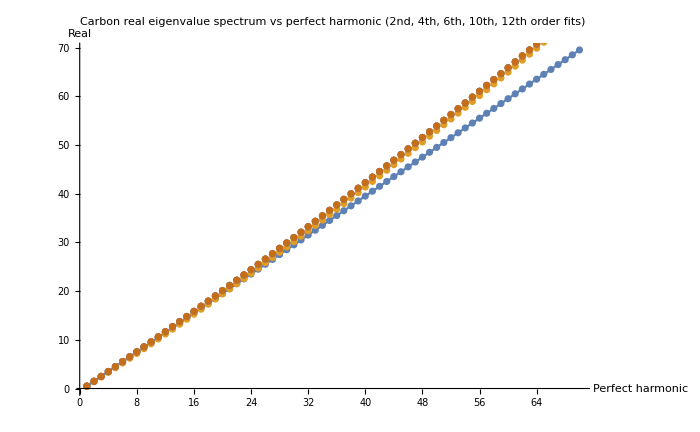

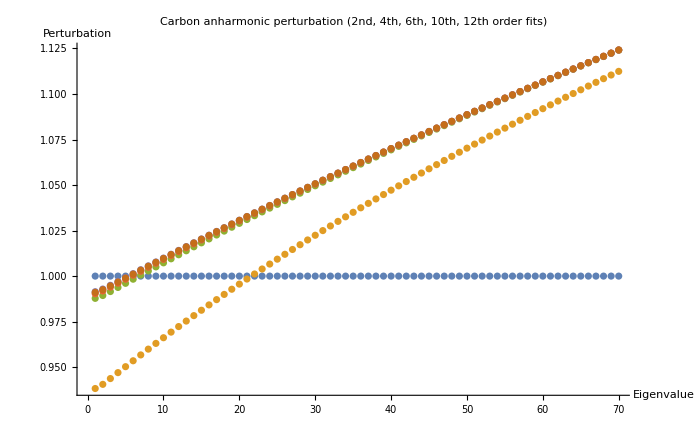

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.469135 | 1.41084 | 2.35933 | 3.31448 | 4.27617 | 5.24427 | 6.21866 | 7.19924 | 8.1859 | 9.17854 | 10.1771 | 11.1814 | 12.1914 | 13.207 | 14.2282 | 15.2548 | 16.2868 | 17.3241 | 18.3666 | 19.4143 | 20.4671 | 21.5249 | 22.5877 | 23.6555 | 24.728 | 25.8054 | 26.8875 | 27.9743 | 29.0657 | 30.1617 | 31.2623 | 32.3673 | 33.4768 | 34.5907 | 35.7089 | 36.8315 | 37.9583 | 39.0894 | 40.2246 | 41.364 | 42.5075 | 43.6551 | 44.8067 | 45.9623 | 47.1219 | 48.2855 | 49.4529 | 50.6242 | 51.7994 | 52.9783 | 54.161 | 55.3475 | 56.5377 | 57.7316 | 58.9292 | 60.1303 | 61.3351 | 62.5435 | 63.7554 | 64.9709 | 66.1898 | 67.4123 | 68.6382 | 69.8675 | 71.1003 | 72.3364 | 73.5759 | 74.8187 | 76.0649 | 77.3143
0.49389 | 1.48401 | 2.47879 | 3.47819 | 4.48216 | 5.49067 | 6.50367 | 7.52112 | 8.54299 | 9.56924 | 10.5998 | 11.6347 | 12.6739 | 13.7173 | 14.7649 | 15.8167 | 16.8726 | 17.9327 | 18.9968 | 20.065 | 21.1371 | 22.2133 | 23.2935 | 24.3776 | 25.4656 | 26.5575 | 27.6532 | 28.7528 | 29.8562 | 30.9634 | 32.0743 | 33.189 | 34.3074 | 35.4295 | 36.5552 | 37.6846 | 38.8177 | 39.9543 | 41.0946 | 42.2384 | 43.3857 | 44.5366 | 45.691 | 46.8488 | 48.0102 | 49.175 | 50.3432 | 51.5148 | 52.6899 | 53.8683 | 55.0501 | 56.2352 | 57.4237 | 58.6154 | 59.8105 | 61.0089 | 62.2105 | 63.4154 | 64.6235 | 65.8348 | 67.0493 | 68.2671 | 69.488 | 70.712 | 71.9392 | 73.1696 | 74.4031 | 75.6396 | 76.8793 | 78.1221
0.495183 | 1.4878 | 2.48491 | 3.48648 | 4.49246 | 5.50283 | 6.51756 | 7.5366 | 8.55994 | 9.58753 | 10.6194 | 11.6554 | 12.6956 | 13.7399 | 14.7883 | 15.8409 | 16.8975 | 17.9581 | 19.0227 | 20.0913 | 21.1639 | 22.2404 | 23.3207 | 24.405 | 25.4932 | 26.5851 | 27.6809 | 28.7805 | 29.8838 | 30.9909 | 32.1017 | 33.2162 | 34.3344 | 35.4562 | 36.5817 | 37.7108 | 38.8435 | 39.9798 | 41.1197 | 42.2631 | 43.41 | 44.5604 | 45.7144 | 46.8718 | 48.0326 | 49.1969 | 50.3647 | 51.5358 | 52.7103 | 53.8882 | 55.0695 | 56.254 | 57.442 | 58.6332 | 59.8277 | 61.0255 | 62.2265 | 63.4309 | 64.6384 | 65.8492 | 67.0631 | 68.2803 | 69.5007 | 70.7242 | 71.9508 | 73.1806 | 74.4136 | 75.6496 | 76.8888 | 78.131
0.495711 | 1.48933 | 2.48734 | 3.4897 | 4.4964 | 5.5074 | 6.52267 | 7.54219 | 8.56593 | 9.59387 | 10.626 | 11.6622 | 12.7026 | 13.7471 | 14.7956 | 15.8482 | 16.9048 | 17.9654 | 19.03 | 20.0985 | 21.171 | 22.2474 | 23.3276 | 24.4118 | 25.4997 | 26.5915 | 27.6871 | 28.7865 | 29.8896 | 30.9964 | 32.107 | 33.2213 | 34.3392 | 35.4608 | 36.5861 | 37.7149 | 38.8474 | 39.9834 | 41.1231 | 42.2662 | 43.4129 | 44.5631 | 45.7168 | 46.874 | 48.0346 | 49.1987 | 50.3662 | 51.5371 | 52.7114 | 53.8891 | 55.0702 | 56.2546 | 57.4423 | 58.6334 | 59.8277 | 61.0254 | 62.2263 | 63.4304 | 64.6379 | 65.8485 | 67.0623 | 68.2794 | 69.4996 | 70.7231 | 71.9496 | 73.1793 | 74.4122 | 75.6482 | 76.8872 | 78.1294
0.495526 | 1.4888 | 2.48652 | 3.48864 | 4.49514 | 5.50597 | 6.52112 | 7.54054 | 8.56421 | 9.59211 | 10.6242 | 11.6605 | 12.7008 | 13.7453 | 14.7939 | 15.8466 | 16.9032 | 17.9639 | 19.0286 | 20.0972 | 21.1697 | 22.2462 | 23.3266 | 24.4108 | 25.4988 | 26.5907 | 27.6864 | 28.7858 | 29.889 | 30.996 | 32.1066 | 33.221 | 34.339 | 35.4607 | 36.586 | 37.715 | 38.8475 | 39.9836 | 41.1233 | 42.2665 | 43.4132 | 44.5635 | 45.7172 | 46.8744 | 48.0351 | 49.1992 | 50.3667 | 51.5377 | 52.712 | 53.8897 | 55.0708 | 56.2552 | 57.4429 | 58.634 | 59.8283 | 61.0259 | 62.2268 | 63.431 | 64.6384 | 65.849 | 67.0628 | 68.2799 | 69.5001 | 70.7235 | 71.95 | 73.1797 | 74.4125 | 75.6485 | 76.8875 | 78.1296

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.93827 | 0.940557 | 0.943732 | 0.946996 | 0.95026 | 0.953503 | 0.956717 | 0.959899 | 0.963047 | 0.966162 | 0.969244 | 0.972293 | 0.975311 | 0.978297 | 0.981254 | 0.98418 | 0.987078 | 0.989948 | 0.99279 | 0.995606 | 0.998396 | 1.00116 | 1.0039 | 1.00662 | 1.00931 | 1.01198 | 1.01462 | 1.01725 | 1.01985 | 1.02243 | 1.02499 | 1.02753 | 1.03006 | 1.03256 | 1.03504 | 1.03751 | 1.03995 | 1.04238 | 1.0448 | 1.04719 | 1.04957 | 1.05193 | 1.05428 | 1.05661 | 1.05892 | 1.06122 | 1.0635 | 1.06577 | 1.06803 | 1.07027 | 1.0725 | 1.07471 | 1.07691 | 1.0791 | 1.08127 | 1.08343 | 1.08558 | 1.08771 | 1.08984 | 1.09195 | 1.09405 | 1.09613 | 1.09821 | 1.10028 | 1.10233 | 1.10437 | 1.1064 | 1.10843 | 1.11044 | 1.11244
0.98778 | 0.989341 | 0.991517 | 0.993769 | 0.996037 | 0.998304 | 1.00056 | 1.00282 | 1.00506 | 1.00729 | 1.00951 | 1.01172 | 1.01391 | 1.0161 | 1.01827 | 1.02043 | 1.02258 | 1.02472 | 1.02685 | 1.02897 | 1.03108 | 1.03318 | 1.03527 | 1.03734 | 1.03941 | 1.04147 | 1.04352 | 1.04556 | 1.04759 | 1.04961 | 1.05162 | 1.05362 | 1.05561 | 1.0576 | 1.05957 | 1.06154 | 1.0635 | 1.06545 | 1.06739 | 1.06933 | 1.07125 | 1.07317 | 1.07508 | 1.07698 | 1.07888 | 1.08077 | 1.08265 | 1.08452 | 1.08639 | 1.08825 | 1.0901 | 1.09195 | 1.09378 | 1.09562 | 1.09744 | 1.09926 | 1.10107 | 1.10288 | 1.10467 | 1.10647 | 1.10825 | 1.11003 | 1.11181 | 1.11358 | 1.11534 | 1.11709 | 1.11884 | 1.12059 | 1.12233 | 1.12406
0.990366 | 0.991868 | 0.993965 | 0.996136 | 0.998324 | 1.00051 | 1.0027 | 1.00488 | 1.00705 | 1.00921 | 1.01137 | 1.01351 | 1.01565 | 1.01777 | 1.01989 | 1.02199 | 1.02409 | 1.02618 | 1.02825 | 1.03032 | 1.03238 | 1.03444 | 1.03648 | 1.03851 | 1.04054 | 1.04255 | 1.04456 | 1.04656 | 1.04855 | 1.05054 | 1.05251 | 1.05448 | 1.05644 | 1.05839 | 1.06034 | 1.06228 | 1.06421 | 1.06613 | 1.06804 | 1.06995 | 1.07185 | 1.07375 | 1.07563 | 1.07751 | 1.07939 | 1.08125 | 1.08311 | 1.08496 | 1.08681 | 1.08865 | 1.09048 | 1.09231 | 1.09413 | 1.09595 | 1.09776 | 1.09956 | 1.10135 | 1.10315 | 1.10493 | 1.10671 | 1.10848 | 1.11025 | 1.11201 | 1.11377 | 1.11552 | 1.11726 | 1.119 | 1.12073 | 1.12246 | 1.12419
0.991422 | 0.992888 | 0.994936 | 0.997058 | 0.9992 | 1.00134 | 1.00349 | 1.00563 | 1.00776 | 1.00988 | 1.012 | 1.01411 | 1.01621 | 1.0183 | 1.02039 | 1.02247 | 1.02453 | 1.0266 | 1.02865 | 1.03069 | 1.03273 | 1.03476 | 1.03678 | 1.0388 | 1.04081 | 1.0428 | 1.0448 | 1.04678 | 1.04876 | 1.05073 | 1.05269 | 1.05464 | 1.05659 | 1.05853 | 1.06047 | 1.06239 | 1.06431 | 1.06623 | 1.06813 | 1.07003 | 1.07192 | 1.07381 | 1.07569 | 1.07756 | 1.07943 | 1.08129 | 1.08314 | 1.08499 | 1.08683 | 1.08867 | 1.0905 | 1.09232 | 1.09414 | 1.09595 | 1.09776 | 1.09956 | 1.10135 | 1.10314 | 1.10492 | 1.1067 | 1.10847 | 1.11023 | 1.11199 | 1.11375 | 1.1155 | 1.11724 | 1.11898 | 1.12071 | 1.12244 | 1.12416
0.991052 | 0.992537 | 0.994609 | 0.996755 | 0.998919 | 1.00109 | 1.00325 | 1.00541 | 1.00755 | 1.0097 | 1.01183 | 1.01395 | 1.01607 | 1.01817 | 1.02027 | 1.02236 | 1.02444 | 1.02651 | 1.02857 | 1.03063 | 1.03267 | 1.03471 | 1.03674 | 1.03876 | 1.04077 | 1.04277 | 1.04477 | 1.04676 | 1.04874 | 1.05071 | 1.05268 | 1.05463 | 1.05659 | 1.05853 | 1.06046 | 1.06239 | 1.06431 | 1.06623 | 1.06814 | 1.07004 | 1.07193 | 1.07382 | 1.0757 | 1.07757 | 1.07944 | 1.0813 | 1.08316 | 1.085 | 1.08685 | 1.08868 | 1.09051 | 1.09233 | 1.09415 | 1.09596 | 1.09777 | 1.09957 | 1.10136 | 1.10315 | 1.10493 | 1.10671 | 1.10848 | 1.11024 | 1.112 | 1.11376 | 1.1155 | 1.11725 | 1.11899 | 1.12072 | 1.12245 | 1.12417

```mathematica
Carbon - look at harmonic and anharmonic eigenvalues;
(*Omega=31.58754341976066;M=12;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)

Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Carbon real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergies,ImageSize->700]
Show[ListPlot[relativeEigenval,PlotLabel->"Carbon anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}],ImageSize->700]

eigenEnergies//TableForm
relativeEigenval//TableForm
```

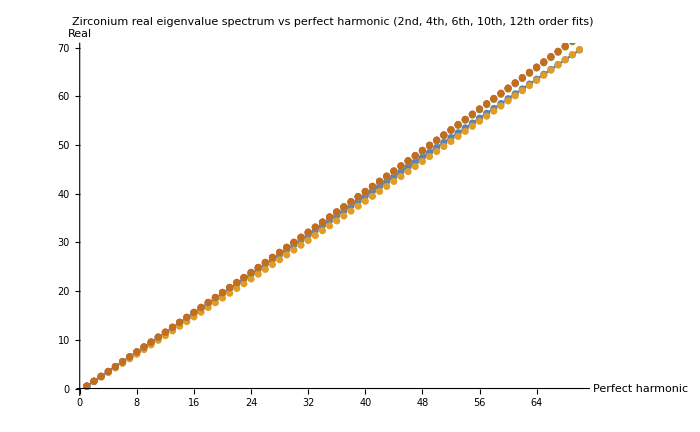

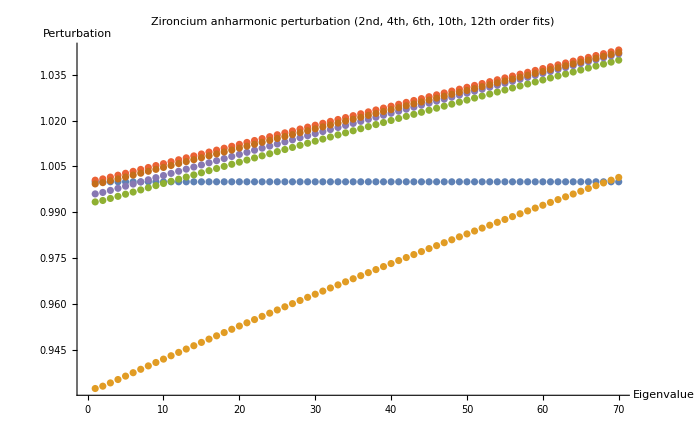

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.466267 | 1.39995 | 2.33591 | 3.27413 | 4.21461 | 5.15731 | 6.10224 | 7.04938 | 7.99871 | 8.95021 | 9.90388 | 10.8597 | 11.8176 | 12.7777 | 13.7399 | 14.7042 | 15.6706 | 16.639 | 17.6095 | 18.5821 | 19.5566 | 20.5332 | 21.5119 | 22.4925 | 23.4751 | 24.4597 | 25.4463 | 26.4348 | 27.4253 | 28.4177 | 29.412 | 30.4083 | 31.4065 | 32.4065 | 33.4085 | 34.4123 | 35.418 | 36.4255 | 37.435 | 38.4462 | 39.4593 | 40.4742 | 41.4909 | 42.5094 | 43.5297 | 44.5519 | 45.5757 | 46.6014 | 47.6288 | 48.658 | 49.689 | 50.7216 | 51.756 | 52.7922 | 53.83 | 54.8696 | 55.9108 | 56.9538 | 57.9985 | 59.0448 | 60.0928 | 61.1424 | 62.1938 | 63.2468 | 64.3014 | 65.3577 | 66.4156 | 67.4751 | 68.5362 | 69.599
0.496715 | 1.49086 | 2.48642 | 3.4834 | 4.48179 | 5.48159 | 6.4828 | 7.48542 | 8.48943 | 9.49484 | 10.5016 | 11.5098 | 12.5194 | 13.5304 | 14.5427 | 15.5565 | 16.5715 | 17.588 | 18.6058 | 19.625 | 20.6456 | 21.6675 | 22.6908 | 23.7154 | 24.7414 | 25.7687 | 26.7974 | 27.8274 | 28.8587 | 29.8914 | 30.9254 | 31.9607 | 32.9973 | 34.0353 | 35.0746 | 36.1152 | 37.1571 | 38.2004 | 39.2449 | 40.2908 | 41.3379 | 42.3864 | 43.4361 | 44.4872 | 45.5395 | 46.5931 | 47.648 | 48.7042 | 49.7617 | 50.8204 | 51.8804 | 52.9417 | 54.0043 | 55.0681 | 56.1332 | 57.1996 | 58.2672 | 59.3361 | 60.4063 | 61.4776 | 62.5503 | 63.6242 | 64.6993 | 65.7757 | 66.8533 | 67.9322 | 69.0123 | 70.0936 | 71.1761 | 72.2599
0.500261 | 1.50142 | 2.50385 | 3.50754 | 4.51251 | 5.51874 | 6.52624 | 7.535 | 8.54503 | 9.55632 | 10.5689 | 11.5827 | 12.5977 | 13.6141 | 14.6316 | 15.6505 | 16.6705 | 17.6919 | 18.7145 | 19.7383 | 20.7634 | 21.7897 | 22.8173 | 23.8461 | 24.8761 | 25.9074 | 26.9399 | 27.9737 | 29.0087 | 30.045 | 31.0824 | 32.1211 | 33.1611 | 34.2022 | 35.2446 | 36.2882 | 37.3331 | 38.3791 | 39.4264 | 40.4749 | 41.5246 | 42.5756 | 43.6277 | 44.6811 | 45.7357 | 46.7915 | 47.8485 | 48.9067 | 49.9661 | 51.0268 | 52.0886 | 53.1516 | 54.2159 | 55.2813 | 56.3479 | 57.4158 | 58.4848 | 59.555 | 60.6265 | 61.6991 | 62.7729 | 63.8479 | 64.924 | 66.0014 | 67.0799 | 68.1597 | 69.2406 | 70.3227 | 71.4059 | 72.4904
0.498027 | 1.49479 | 2.49297 | 3.49255 | 4.49355 | 5.49595 | 6.49974 | 7.50493 | 8.5115 | 9.51947 | 10.5288 | 11.5395 | 12.5516 | 13.5651 | 14.5799 | 15.5961 | 16.6137 | 17.6326 | 18.6528 | 19.6744 | 20.6974 | 21.7216 | 22.7473 | 23.7742 | 24.8025 | 25.8321 | 26.863 | 27.8953 | 28.9288 | 29.9637 | 30.9999 | 32.0374 | 33.0762 | 34.1163 | 35.1577 | 36.2004 | 37.2443 | 38.2896 | 39.3361 | 40.384 | 41.4331 | 42.4834 | 43.5351 | 44.588 | 45.6422 | 46.6976 | 47.7544 | 48.8123 | 49.8716 | 50.932 | 51.9938 | 53.0567 | 54.121 | 55.1864 | 56.2531 | 57.3211 | 58.3902 | 59.4606 | 60.5323 | 61.6051 | 62.6792 | 63.7545 | 64.831 | 65.9088 | 66.9877 | 68.0679 | 69.1493 | 70.2319 | 71.3157 | 72.4006
0.499655 | 1.4996 | 2.5008 | 3.50327 | 4.507 | 5.51199 | 6.51825 | 7.52577 | 8.53456 | 9.5446 | 10.5559 | 11.5685 | 12.5823 | 13.5974 | 14.6138 | 15.6314 | 16.6503 | 17.6704 | 18.6918 | 19.7145 | 20.7384 | 21.7636 | 22.79 | 23.8177 | 24.8466 | 25.8768 | 26.9083 | 27.941 | 28.9749 | 30.0101 | 31.0466 | 32.0843 | 33.1232 | 34.1634 | 35.2048 | 36.2475 | 37.2915 | 38.3366 | 39.383 | 40.4307 | 41.4796 | 42.5297 | 43.5811 | 44.6337 | 45.6875 | 46.7426 | 47.7989 | 48.8564 | 49.9151 | 50.9751 | 52.0363 | 53.0987 | 54.1624 | 55.2273 | 56.2934 | 57.3607 | 58.4292 | 59.4989 | 60.5699 | 61.6421 | 62.7155 | 63.79 | 64.8658 | 65.9429 | 67.0211 | 68.1005 | 69.1811 | 70.2629 | 71.3459 | 72.4301

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.932534 | 0.933297 | 0.934362 | 0.935466 | 0.936579 | 0.937694 | 0.938807 | 0.939917 | 0.941024 | 0.942127 | 0.943226 | 0.944321 | 0.945412 | 0.946498 | 0.94758 | 0.948657 | 0.949731 | 0.9508 | 0.951865 | 0.952926 | 0.953982 | 0.955035 | 0.956083 | 0.957128 | 0.958168 | 0.959204 | 0.960237 | 0.961266 | 0.962291 | 0.963312 | 0.964329 | 0.965342 | 0.966352 | 0.967359 | 0.968361 | 0.96936 | 0.970356 | 0.971348 | 0.972336 | 0.973321 | 0.974303 | 0.975281 | 0.976256 | 0.977228 | 0.978196 | 0.979161 | 0.980123 | 0.981082 | 0.982038 | 0.98299 | 0.983939 | 0.984886 | 0.985829 | 0.986769 | 0.987706 | 0.988641 | 0.989572 | 0.990501 | 0.991426 | 0.992349 | 0.993269 | 0.994186 | 0.9951 | 0.996011 | 0.99692 | 0.997826 | 0.99873 | 0.99963 | 1.00053 | 1.00142
0.993429 | 0.993903 | 0.994567 | 0.995256 | 0.995953 | 0.996653 | 0.997354 | 0.998056 | 0.998757 | 0.999457 | 1.00016 | 1.00086 | 1.00155 | 1.00225 | 1.00295 | 1.00364 | 1.00434 | 1.00503 | 1.00572 | 1.00641 | 1.0071 | 1.00779 | 1.00848 | 1.00917 | 1.00985 | 1.01054 | 1.01122 | 1.0119 | 1.01259 | 1.01327 | 1.01395 | 1.01463 | 1.0153 | 1.01598 | 1.01666 | 1.01733 | 1.018 | 1.01868 | 1.01935 | 1.02002 | 1.02069 | 1.02136 | 1.02203 | 1.02269 | 1.02336 | 1.02402 | 1.02469 | 1.02535 | 1.02601 | 1.02667 | 1.02734 | 1.02799 | 1.02865 | 1.02931 | 1.02997 | 1.03062 | 1.03128 | 1.03193 | 1.03259 | 1.03324 | 1.03389 | 1.03454 | 1.03519 | 1.03584 | 1.03648 | 1.03713 | 1.03778 | 1.03842 | 1.03907 | 1.03971
1.00052 | 1.00095 | 1.00154 | 1.00216 | 1.00278 | 1.00341 | 1.00404 | 1.00467 | 1.0053 | 1.00593 | 1.00656 | 1.00719 | 1.00782 | 1.00845 | 1.00908 | 1.00971 | 1.01034 | 1.01096 | 1.01159 | 1.01222 | 1.01285 | 1.01347 | 1.0141 | 1.01473 | 1.01535 | 1.01598 | 1.0166 | 1.01723 | 1.01785 | 1.01847 | 1.0191 | 1.01972 | 1.02034 | 1.02096 | 1.02158 | 1.0222 | 1.02282 | 1.02344 | 1.02406 | 1.02468 | 1.0253 | 1.02592 | 1.02653 | 1.02715 | 1.02777 | 1.02838 | 1.029 | 1.02961 | 1.03023 | 1.03084 | 1.03146 | 1.03207 | 1.03268 | 1.0333 | 1.03391 | 1.03452 | 1.03513 | 1.03574 | 1.03635 | 1.03696 | 1.03757 | 1.03818 | 1.03878 | 1.03939 | 1.04 | 1.0406 | 1.04121 | 1.04182 | 1.04242 | 1.04303
0.996054 | 0.996526 | 0.997187 | 0.997873 | 0.998566 | 0.999263 | 0.99996 | 1.00066 | 1.00135 | 1.00205 | 1.00274 | 1.00344 | 1.00413 | 1.00482 | 1.00551 | 1.0062 | 1.00689 | 1.00757 | 1.00826 | 1.00894 | 1.00963 | 1.01031 | 1.01099 | 1.01167 | 1.01235 | 1.01302 | 1.0137 | 1.01437 | 1.01505 | 1.01572 | 1.01639 | 1.01706 | 1.01773 | 1.0184 | 1.01906 | 1.01973 | 1.02039 | 1.02106 | 1.02172 | 1.02238 | 1.02304 | 1.0237 | 1.02435 | 1.02501 | 1.02567 | 1.02632 | 1.02698 | 1.02763 | 1.02828 | 1.02893 | 1.02958 | 1.03023 | 1.03087 | 1.03152 | 1.03217 | 1.03281 | 1.03345 | 1.0341 | 1.03474 | 1.03538 | 1.03602 | 1.03666 | 1.0373 | 1.03793 | 1.03857 | 1.0392 | 1.03984 | 1.04047 | 1.0411 | 1.04174
0.99931 | 0.999731 | 1.00032 | 1.00093 | 1.00156 | 1.00218 | 1.00281 | 1.00344 | 1.00407 | 1.0047 | 1.00533 | 1.00596 | 1.00659 | 1.00722 | 1.00785 | 1.00848 | 1.00911 | 1.00974 | 1.01037 | 1.011 | 1.01163 | 1.01226 | 1.01289 | 1.01352 | 1.01415 | 1.01478 | 1.01541 | 1.01603 | 1.01666 | 1.01729 | 1.01792 | 1.01855 | 1.01918 | 1.0198 | 1.02043 | 1.02106 | 1.02168 | 1.02231 | 1.02294 | 1.02356 | 1.02419 | 1.02481 | 1.02544 | 1.02606 | 1.02668 | 1.02731 | 1.02793 | 1.02855 | 1.02918 | 1.0298 | 1.03042 | 1.03104 | 1.03166 | 1.03228 | 1.03291 | 1.03353 | 1.03414 | 1.03476 | 1.03538 | 1.036 | 1.03662 | 1.03724 | 1.03785 | 1.03847 | 1.03909 | 1.0397 | 1.04032 | 1.04093 | 1.04155 | 1.04216

```mathematica
Zirconium - look at harmonic and anharmonic eigenvalues;
(*zOmega=13.44788050977517;M=91;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)

Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Zirconium real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergiesZ,ImageSize->700]
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
Show[ListPlot[relativeEigenvalz,ImageSize->700,PlotLabel->"Zironcium anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}]]

eigenEnergiesZ//TableForm
relativeEigenvalz//TableForm
```

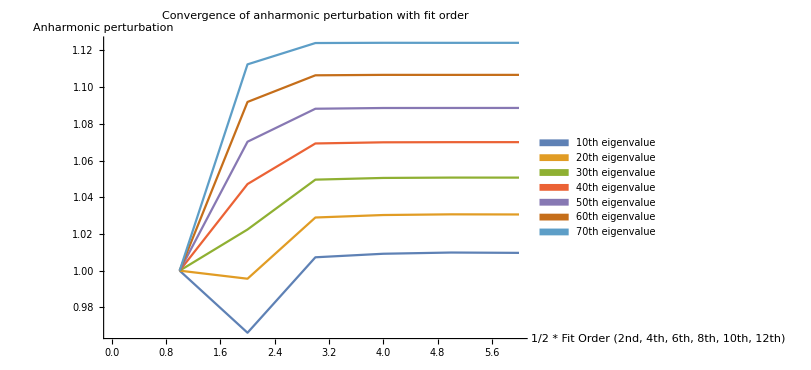

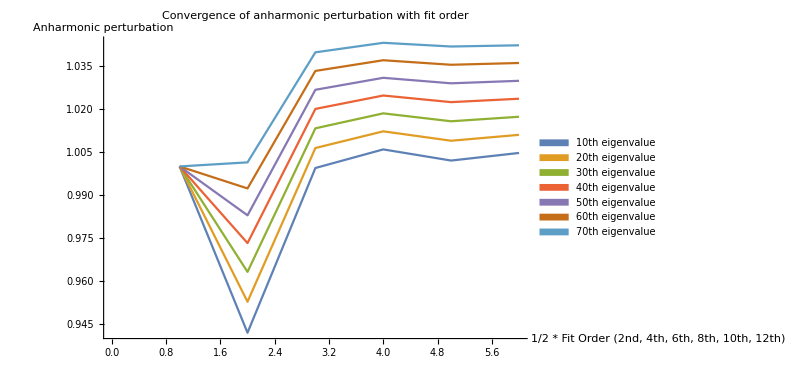

```mathematica
Carbon and zirconium - check convergence of eigenvalues with fit order;
plotstuff={ImageSize->600,PlotLegends->SwatchLegend[{"10th eigenvalue","20th eigenvalue","30th eigenvalue","40th eigenvalue","50th eigenvalue","60th eigenvalue","70th eigenvalue"}],PlotLabel->"Convergence of anharmonic perturbation with fit order",AxesLabel->{"1/2 * Fit Order \n(2nd, 4th, 6th, 8th, 10th, 12th)","Anharmonic\nperturbation"}};
ListPlot[Table[Transpose[relativeEigenval][[i]],{i,10,70,10}], Joined->True,plotstuff]
ListPlot[Table[Transpose[relativeEigenvalz][[i]],{i,10,70,10}], Joined->True,plotstuff]
```

```mathematica
Plot input stuff for Carbon eigensystem;
(*eigenPlots=Table[Show[Plot[Evaluate[(6*eigensysC[[i]][[2]])+eigensysC[[i]][[1]]],{x,-B,B}],Plot[Evaluate@V[1,2i,x],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};*)
```

```mathematica
Plot carbon potential and eigensystem (eigenvectors and eigenvectors*eigenvalues);
(*GraphicsGrid[plotgrid,ImageSize->1100]*)
```

```mathematica
Plot input stuff for Zr eigensystem;
(*Bz=0.5;Hz=1000;
eigenPlotsz=Table[Show[Plot[Evaluate[(4*eigensysZ[[i]][[2]])+eigensysZ[[i]][[1]]],{x,-Bz,Bz}],Plot[Evaluate@V[2,2i,x],{x,-Bz,Bz}],PlotRange->{{-Bz,Bz},{0,Hz}},AxesOrigin->{-Bz,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
plotgridz={Table[eigenPlotsz[[i]],{i,1,2}],Table[eigenPlotsz[[j]],{j,3,4}],Table[eigenPlotsz[[k]],{k,5,6}]};*)
```

```mathematica
Plot zirconium eigensystem;
(*GraphicsGrid[plotgridz,ImageSize->1100]*)
```

0.991446+0.00193208 x

0.988591+0.00217 x-3.35098×10^-6 x^2

0.988549+0.00217695 x-3.59393×10^-6 x^2+2.28123×10^-9 x^3

0.988707+0.00213508 x-9.84271×10^-7 x^2-5.4621×10^-8 x^3+4.0072×10^-10 x^4

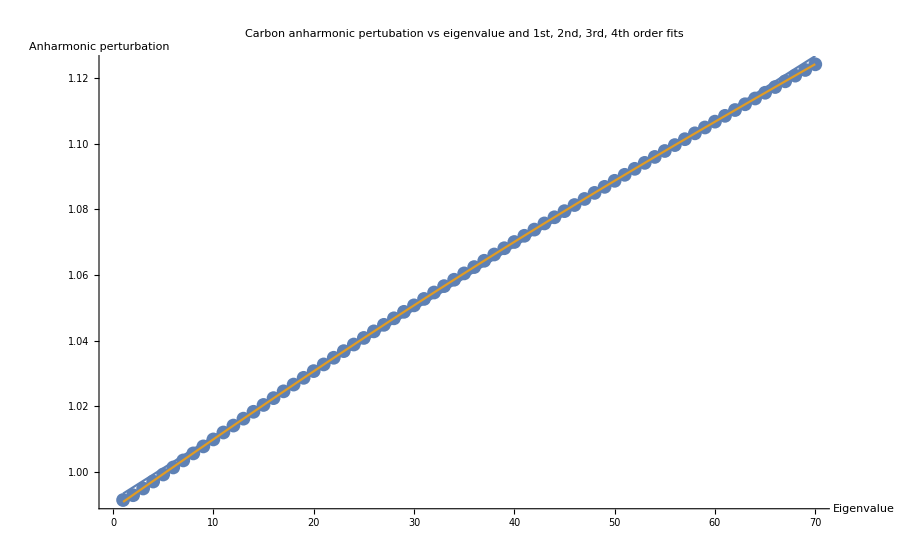

```mathematica
Carbon - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1=Fit[relativeEigenval[[5]],{1,x},x]
anharmonicfit2=Fit[relativeEigenval[[5]],{1, x, x^2},x]
anharmonicfit3=Fit[relativeEigenval[[5]],{1, x, x^2,x^3},x]
anharmonicfit4=Fit[relativeEigenval[[5]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ImageSize->900]
```

```mathematica
Zirconium - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1z=Fit[relativeEigenvalz[[6]],{1,x},x]
anharmonicfit2z=Fit[relativeEigenvalz[[6]],{1, x, x^2},x]
anharmonicfit3z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3},x]
anharmonicfit4z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenvalz[[6]],PlotLabel->"Zirconium anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

Null Zirconium

0.998497+0.000625304 x

0.998417+0.000631966 x-9.38253×10^-8 x^2

0.998535+0.00060755 x+1.13021×10^-6 x^2-2.19648×10^-8 x^3+1.29516×10^-10 x^4

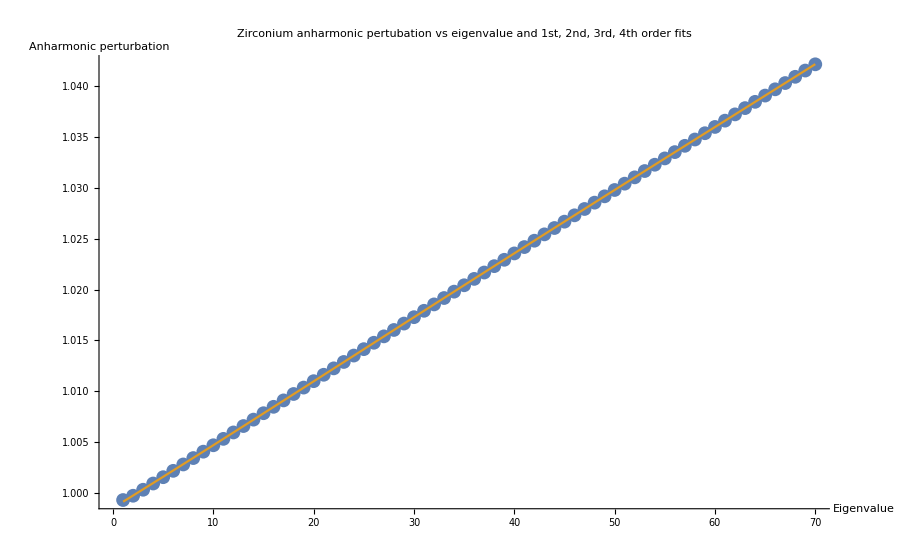

```mathematica
0.9984840779371645+0.0006210804635938045 x+2.867500483226181*^-7 x^2-3.573477223788385*^-9 x^3
```

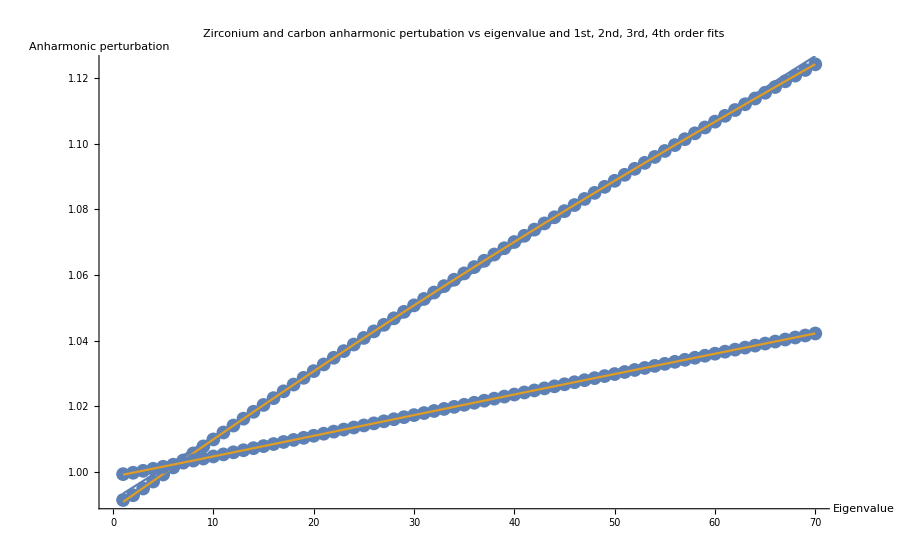

```mathematica
(*Compare C and Zr anharmonic perturbations*)
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Zirconium and carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ListPlot[relativeEigenvalz[[6]]],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

```mathematica
(*Plot derivitive of C and Zr anharmonic perturbation fits*)
(*cAnharmonicityDerivitive=D[{anharmonicfit1,anharmonicfit2,anharmonicfit3,anharmonicfit4},x]
zrAnharmonicityDerivitive=D[{anharmonicfit1z,anharmonicfit2z,anharmonicfit3z,anharmonicfit4z},x]
GraphicsGrid[{{Show@Plot[{cAnharmonicityDerivitive},{x,0,70},ImageSize->400],Show@Plot[{zrAnharmonicityDerivitive},{x,0,70}]}}]*)
```

```mathematica
(*Calculate partition function and Helmholtz free energy with Einstein frequencies*)
(*As previous, define omega0 as the solution to A*x*x=1/2*m*omega*omega*x*x, where A*x*x is the harmonic fit*)
"4.685Ang Einstein frequencies from polynomial fit:"
Acarbon=V[1,2,X][[1]];
cOmega0=Sqrt[2Acarbon/m[[1]]]
Azirconium=V[2,2,X][[1]];
zOmega0=Sqrt[2Azirconium/m[[2]]] 
(*Note, if we define the Einstein frequency in terms of the QHA DOS as the energy integrating up to which gives the number of modes equal to the 3*Natoms/2, then the frequencies are*)
"4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:"
cOmegaInt48=65.1879672429008/2
zrOmegaInt48=26.329538754361874/2
"4.685Ang Einstein frequencies from QHA finding peak frequency for each band:"
cOmegaMaxPeak=4.14*18.0295229515/2
zrOmegaMaxPeak=4.14*6.2446881878/2
```

4.685Ang Einstein frequencies from polynomial fit:

29.2063

12.0443

4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:

32.594

13.1648

4.685Ang Einstein frequencies from QHA finding peak frequency for each band:

37.3211

12.9265

```mathematica
(*Zirconium eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.499655 | 1.4996 | 2.5008 | 3.50327 | 4.507 | 5.51199 | 6.51825 | 7.52577 | 8.53456 | 9.5446 | 10.5559 | 11.5685 | 12.5823 | 13.5974 | 14.6138
15.6314 | 16.6503 | 17.6704 | 18.6918 | 19.7145 | 20.7384 | 21.7636 | 22.79 | 23.8177 | 24.8466 | 25.8768 | 26.9083 | 27.941 | 28.9749 | 30.0101
31.0466 | 32.0843 | 33.1232 | 34.1634 | 35.2048 | 36.2475 | 37.2915 | 38.3366 | 39.383 | 40.4307 | 41.4796 | 42.5297 | 43.5811 | 44.6337 | 45.6875
46.7426 | 47.7989 | 48.8564 | 49.9151 | 50.9751 | 52.0363 | 53.0987 | 54.1624 | 55.2273 | 56.2934 | 57.3607 | 58.4292 | 59.4989 | 60.5699 | 61.6421

```mathematica
(*Carbon eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.495526 | 1.4888 | 2.48652 | 3.48864 | 4.49514 | 5.50597 | 6.52112 | 7.54054 | 8.56421 | 9.59211 | 10.6242 | 11.6605 | 12.7008 | 13.7453 | 14.7939
15.8466 | 16.9032 | 17.9639 | 19.0286 | 20.0972 | 21.1697 | 22.2462 | 23.3266 | 24.4108 | 25.4988 | 26.5907 | 27.6864 | 28.7858 | 29.889 | 30.996
32.1066 | 33.221 | 34.339 | 35.4607 | 36.586 | 37.715 | 38.8475 | 39.9836 | 41.1233 | 42.2665 | 43.4132 | 44.5635 | 45.7172 | 46.8744 | 48.0351
49.1992 | 50.3667 | 51.5377 | 52.712 | 53.8897 | 55.0708 | 56.2552 | 57.4429 | 58.634 | 59.8283 | 61.0259 | 62.2268 | 63.431 | 64.6384 | 65.849

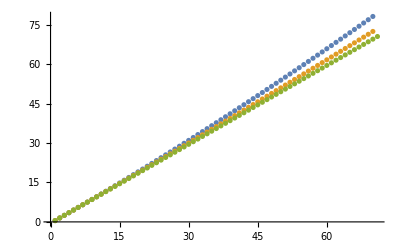

```mathematica
ListPlot[{eigenEnergies[[6]],eigenEnergiesZ[[6]],Table[i+1/2,{i,0,70}]}]
```

```mathematica
(*Define standard harmonic omega argument thermodynamic functions - Helmholtz - entropy - Cv*)
K2meV=0.086173324;
HH[T_,Einsteinlist_]:=1.5*(0.5*Total[Einsteinlist]+K2meV*T*Total[Log[1-Exp[-((Einsteinlist)/(K2meV*T))]]])

SS[T_,Einsteinlist_]:=1.5*((1/(2*T))*Total[Einsteinlist*Coth[(Einsteinlist)/(2*K2meV*T)]]-K2meV*Total[Log[2*Sinh[(Einsteinlist)/(2*K2meV*T)]]])

EE[T_,Einsteinlist_]:=1.5*(Total[(Einsteinlist)/2]+Total[1/(Exp[Einsteinlist/(K2meV*T)]-1)])

CC[T_,Einsteinlist_]:=1.5*Total[K2meV*(((Einsteinlist)/(K2meV*T))^2)*(Exp[Einsteinlist/(K2meV*T)]/((Exp[Einsteinlist/(K2meV*T)]-1)^2))]
```

```mathematica
(*Zero point energies*)
(*QHA 48 mode Einstein oscillators*)
zpeEinstein=HH[0.00001,Einstein4685]
(*QHA *)
zpeQHA4685=thermalData4685[[6]][[1]]
(*Quadratic fit to harmonic Einstein oscillator potential for 4.685*)
1.5*(zOmega0+cOmega0)
```

Total::normal: Nonatomic expression expected at position 1 in Total[Einstein4685].

1.5 (8.61733×10^-7 (1-ⅇ^(-1.16045×10^6 Einstein4685))+0.5 Total[Einstein4685])

Part::partd: Part specification thermalData4685⟦6⟧ is longer than depth of object.

thermalData4685

61.8758

```mathematica
Define a more general partition that takes as argument an arbitary eigenspectrum;
(*Partition function as a power series expansion of eigenspectrum http://www.nyu.edu/classes/tuckerman/stat.mech/lectures/lecture_13/node8.html *)
Zpower[T_,eigenlist_]:=Exp[-eigenlist/(2*K2meV*T)]*Total[Table[Exp[-eigenlist/(K2meV*T)]^k,{k,0,100}]]
Zgen[T_,order_]:={Total[Exp[-2*zOmega0*eigenEnergiesZ[[order]]/(K2meV*T)]],Total[Exp[-2*cOmega0*eigenEnergies[[order]]/(K2meV*T)]]}
```

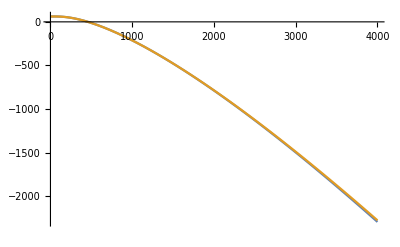

```mathematica
Define free energy of Helmholtz via partition function;
einsteinOmega0=2{zOmega0,cOmega0};
maxEigen=100;
Apower[T_,eigenlist_]:=-K2meV*1.5T*Log[Zpower[T,eigenlist]]
A[T_,1]:=-K2meV*1.5*T*Log[Zgen[T,1]]
A[T_,6]:=-K2meV*1.5*T*Log[Zgen[T,6]]
(*Perfect Einstein Helmholtz Free energy from partition function*)
Define free energy via partition function;
Plot[{Total@Apower[T,einsteinOmega0],Total@A[T,6]},{T,1,4000}]
```

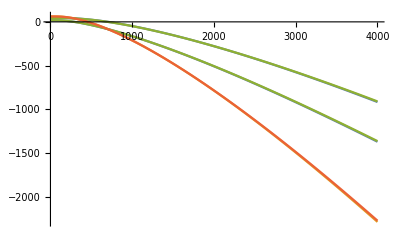

```mathematica
Plot[{{A[T,1],Total@A[T,1]},{A[T,6],Total@A[T,6]}},{T,1,4000}]
```

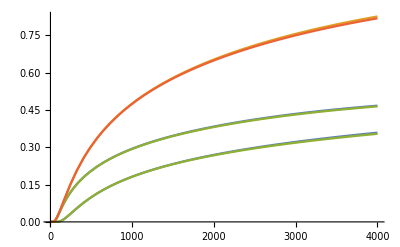

-Graphics-

```mathematica
Define entropy via partition function;
S[T_,order_]:=-D[A[t,order],t]/.t->T
Plot[{{-D[A[t,1],t]/.t->T,Total@-D[A[t,1],t]/.t->T},{-D[A[t,6],t]/.t->T,Total@-D[A[t,6],t]/.t->T}},{T,1,4000}]
Plot[{{S[T,1],Total@S[T,1]},{S[T,6],Total@S[T,6]}},{T,1,4000}]
```

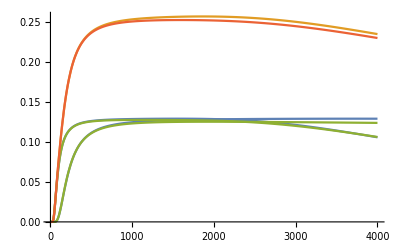

-Graphics-

```mathematica
Define heat capacity via partition function;
Plot[{{-t*D[D[A[t,1],t],t]/.t->T,Total[-t*D[D[A[t,1],t],t]]/.t->T},{-t*D[D[A[t,6],t],t]/.t->T,Total[-t*D[D[A[t,6],t],t]]/.t->T}},{T,1,4000}]

Heat[T_,order_]:=t*D[S[t,order],t]/.t->T
Plot[{{Heat[T,1],Total[Heat[T,1]]},{Heat[T,6],Total[Heat[T,6]]}},{T,1,4000}]
```

```mathematica
spectrumAnharmonicZ= Table[0.5+x*anharmonicfit4z,{x,0,1000}];
spectrumAnharmonicC=Table[0.5+x*anharmonicfit4,{x,0,1000}];
ZanharmonicFit[T_,spectrumZ_,spectrumC_]:={Total[Exp[-2*zOmega0*spectrumZ/(K2meV*T)]],Total[Exp[-2*cOmega0*spectrumC/(K2meV*T)]]}
ZanharmonicFit[T,spectrumAnharmonicZ,spectrumAnharmonicC];
Afit[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZ,spectrumAnharmonicC]]
```

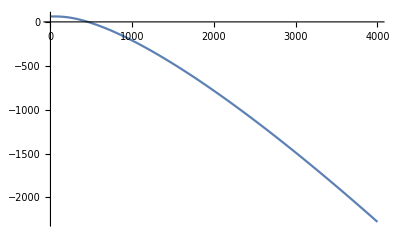

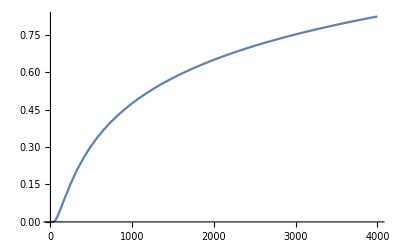

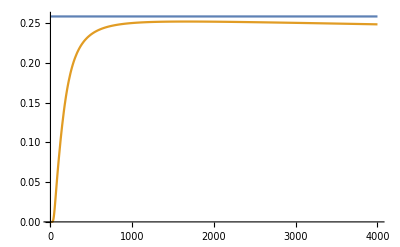

```mathematica
Plot[{Total@Afit[T]},{T,1,4000}]
Plot[{Total@-D[Afit[T],T]/.T->t},{t,1,4000}]
Plot[{K2meV*3,Total[T*D[-D[Afit[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
```

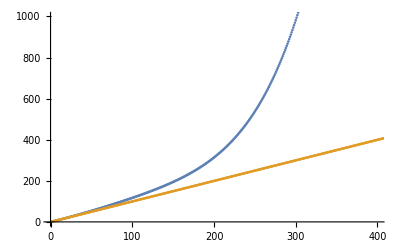

```mathematica
ListPlot[{spectrumAnharmonicC,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,400},{0,1000}}]
```